## RNN Sequence 10

```mathematica
rescaledSubtractedTS=Import["C:\\Users\\kylem\\Documents\\GitHub\\2019-WSS\\Final Project\\Drafts\\kyle\\rescaledsubtractedTS.wxf"]
```

TimeSeries[…]

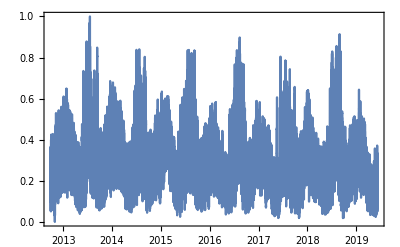

```mathematica
DateListPlot[rescaledSubtractedTS]
```

```mathematica
data=rescaledSubtractedTS//Normal;
```

```mathematica
values=QuantityMagnitude@data[[All,2]];keysp=Partition[values,20,1];valuesp = values[[21;;]];
```

```mathematica
threaddata=Thread[Table[ArrayReshape[keysp[[i]],{1,20}]->valuesp[[i]],{i,1,Length@valuesp}]];
```

```mathematica
Length@data
```

58680

```mathematica
Length@threaddata
```

58660

```mathematica
{trainingdata,testdata}=TakeDrop[threaddata,45000];
```

```mathematica
rnn=NetChain[{GatedRecurrentLayer[32,"Dropout"->{"VariationalInput"->0.3},"Input"->{"Varying",20}],GatedRecurrentLayer[64,"Dropout"->{"VariationalInput"->0.3}],GatedRecurrentLayer[64,"Dropout"->{"VariationalInput"->0.3}],SequenceLastLayer[],LinearLayer[128],Ramp,LinearLayer[1]},"Output"->"Scalar"]
```

NetChain[<>]

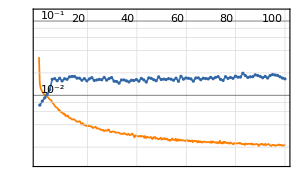
NetTrain Results
summary | ,,  batches:5700  rounds:100  time:5.9min  examples/s:12874
data | ,,  training examples:45000  validation examples:13660  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:2.12×10^-3
validation | ,,  loss:1.66×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set |

```mathematica
trainednet =  NetTrain[rnn,trainingdata,All,ValidationSet->testdata,BatchSize->800,Method-> "ADAM",MaxTrainingRounds->100]
```

```mathematica
AssociationMap[ PredictorMeasurements[
Predict[trainingdata,Method->#,PerformanceGoal->"DirectTraining"],testdata, "MeanSquare"]&,{"RandomForest"}]
```

<|RandomForest→0.000996944|>

```mathematica
SeedRandom[111];rsample=RandomSample[testdata,2]
```

{{{0.369093,0.37334,0.367965,0.35475,0.343098,0.338917,0.340734,0.358589,0.384605,0.397505,0.405578,0.377491,0.323889,0.256743,0.211822,0.188537,0.17249,0.164079,0.165224,0.166897}}→0.207014,{{0.132999,0.113477,0.109631,0.112344,0.131025,0.15343,0.209249,0.252979,0.256041,0.250144,0.256307,0.252906,0.241815,0.257404,0.249385,0.270205,0.296964,0.297775,0.300904,0.316309}}→0.310272}

```mathematica
trainednet[rsample[[2,1]]]
```

NetTrain Results
summary | ,,  batches:5700  rounds:100  time:5.9min  examples/s:12874
data | ,,  training examples:45000  validation examples:13660  processed examples:4560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size800CPU
round | ,,  loss:2.12×10^-3
validation | ,,  loss:1.66×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | [{{0.132999,0.113477,0.109631,0.112344,0.131025,0.15343,0.209249,0.252979,0.256041,0.250144,0.256307,0.252906,0.241815,0.257404,0.249385,0.270205,0.296964,0.297775,0.300904,0.316309}}]

```mathematica
sobj=NetStateObject[trainednet]
```

NetStateObject::arg1: First argument to NetStateObject should be a valid net.

$Failed

```mathematica
results=Union@Flatten@NestList[Drop[Join[#,{trainednet[#]}],1]&,testdata[[1,1]],100]
```

{1}
 |  |  |  |

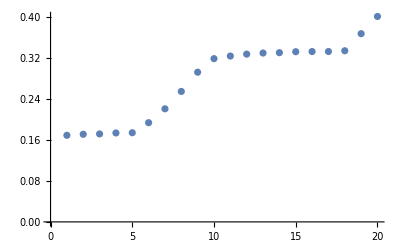

```mathematica
ListPlot[results]
```